# Optimizing welfare on linked supply chains through tariffs.

## Defining market curves

```mathematica
ClearAll[qs,qb ]
```

```mathematica
ClearAll[ a,b,c,d,e,f,g, α]
```

```mathematica
ClearAll[i,t]
```

```mathematica
ClearAll[bs,bb, cs, cb, dbe, dbb,πs,πb]
```

```mathematica
ClearAll[UB, UE]
```

```mathematica
ClearAll[opti, optt]
```

```mathematica
ClearAll[BrOpti,EUOptt]
```

## Basic Mkt functions

```mathematica
bs= a*qs -b*qs^2
```

a qs-b qs^2

```mathematica
bb = c*qb - d*qb^2
```

c qb-d qb^2

```mathematica
cs = e*qs^2
```

e qs^2

```mathematica
cb = D[cs,{qs}]*qb
```

2 e qb qs

```mathematica
dbe =f*qb^2
```

f qb^2

```mathematica
dbb = g*qb^2
```

g qb^2

```mathematica
πs = (D[bs,{qs}]-t)*qs - cs
```

-e qs^2+qs (a-2 b qs-t)

```mathematica
πb = (D[bb,{qb}]-i)*qb - cb
```

qb (c-i-2 d qb)-2 e qb qs

## Country Functions

### Brazil

```mathematica
UB = πs + πb + bb+ α*i*qb -dbb
```

c qb-d qb^2-g qb^2+qb (c-i-2 d qb)-2 e qb qs-e qs^2+qs (a-2 b qs-t)+i qb α

### Eropean Union

```mathematica
UE = bs - D[bs,{qs}]*qs - dbe + qs*t
```

-f qb^2+a qs-b qs^2-qs (a-2 b qs)+qs t

## Solving reaction functions for companies

```mathematica
rb = Solve[(D[bb,{qb}]-i) == D[cb,{qb}],{qb}]
```

{{qb→(c-i-2 e qs)/(2 d)}}

```mathematica
qb=rb[[1]][[1]][[2]]
```

(c-i-2 e qs)/(2 d)

```mathematica
rs = Solve[(D[bs,{qs}]-t) == D[cs,{qs}],{qs}]
```

{{qs→(a-t)/(2 (b+e))}}

```mathematica
qs=rs[[1]][[1]][[2]]
```

(a-t)/(2 (b+e))

### Finding i and t

```mathematica
opti = D[UB, i] == 0
```

-c/(2 d)+(c-i-(e (a-t))/(b+e))/(2 d)+(g (c-i-(e (a-t))/(b+e)))/(2 d^2)-(i α)/(2 d)+((c-i-(e (a-t))/(b+e)) α)/(2 d)==0

```mathematica
rUB = Solve[opti,{i}][[1]][[1]][[2]]
```

(-a d e+b c g-a e g+c e g+d e t+e g t+b c d α-a d e α+c d e α+d e t α)/((b+e) (d+g+2 d α))

```mathematica
Simplify[rUB]
```

(b c (g+d α)+c e (g+d α)-a e (d+g+d α)+e t (d+g+d α))/((b+e) (d+g+2 d α))

```mathematica
Simplify[D[rUB, t]]
```

(e (d+g+d α))/((b+e) (d+g+2 d α))

```mathematica
Simplify[D[rUB, α]]
```

(d (b c (d-g)+e (c (d-g)+a (d+g)-(d+g) t)))/((b+e) (d+g+2 d α)^2)

```mathematica
D[(b c (g+d α)+c e (g+d α)-a e (d+g+d α)+e t (d+g+d α))/((b+e) (d+g+2 d α)), α]
```

(b c d-a d e+c d e+d e t)/((b+e) (d+g+2 d α))-(2 d (b c (g+d α)+c e (g+d α)-a e (d+g+d α)+e t (d+g+d α)))/((b+e) (d+g+2 d α)^2)

```mathematica
Simplify[(b c d-a d e+c d e+d e t)/((b+e) (d+g+2 d α))-(2 d (b c (g+d α)+c e (g+d α)-a e (d+g+d α)+e t (d+g+d α)))/((b+e) (d+g+2 d α)^2)]
```

(d (b c (d-g)+e (c (d-g)+a (d+g)-(d+g) t)))/((b+e) (d+g+2 d α)^2)

```mathematica
optt = D[UE, t] ==0
```

-a/(2 (b+e))+(a-(b (a-t))/(b+e))/(2 (b+e))-(e f (c-i-(e (a-t))/(b+e)))/(2 d^2 (b+e))+(a-t)/(2 (b+e))-t/(2 (b+e))==0

```mathematica
rUE = Solve[optt ,t][[1]][[1]][[2]]
```

((a b)/(2 (b+e)^2)-a/(2 (b+e))-(a e^2 f)/(2 d^2 (b+e)^2)+(c e f)/(2 d^2 (b+e))-(e f i)/(2 d^2 (b+e)))/(b/(2 (b+e)^2)-1/(b+e)-(e^2 f)/(2 d^2 (b+e)^2))

```mathematica
Simplify[rUE]
```

(e (a (d^2+e f)-(b+e) f (c-i)))/(b d^2+e (2 d^2+e f))

```mathematica
D[rUE,i]
```

-(e f)/(2 d^2 (b+e) (b/(2 (b+e)^2)-1/(b+e)-(e^2 f)/(2 d^2 (b+e)^2)))

```mathematica
α = 1; a = 3.5; b = 0.1; c = 3; d =0.6; e = 0.1;f =2.65;  g= 1.14; (*g= 1.14, f = 2.65;*)
sol = Solve[rUB-i ==0 &&rUE - t==0, {i,t}]
```

{{i→0.663487,t→0.705687}}

## Results

#### Benchmark

```mathematica
UE/.{i->0, t->0}
```

4.78082

```mathematica
UB/.{i->0, t->0}
```

8.89323

```mathematica
dbb/.{i->0, t->0}
```

1.23698

```mathematica
dbe/.{i->0, t->0}
```

2.87543

```mathematica
totalwelfare = UE + UB/.{i->0, t->0}
```

13.674

```mathematica
totaldamage = dbb +dbe/.{i->0, t->0}
```

4.11241

```mathematica
qb/.{i->0, t->0}
```

1.04167

```mathematica
qs/.{i->0, t->0}
```

8.75

#### Optimal Tariffs

```mathematica
Simplify[UE/.sol]
```

{8.18605}

```mathematica
Simplify[UB/.sol]
```

{6.68166}

```mathematica
Simplify[dbb/.sol]
```

{0.698558}

```mathematica
dbe/.sol
```

{1.62384}

```mathematica
Simplify[totalwelfare = UE + UB/.sol]
```

{14.8677}

```mathematica
totaldamage = dbb +dbe/.sol
```

{2.3224}

```mathematica
Simplify[qb/.sol]
```

{0.782796}

```mathematica
qs/.sol
```

{6.98578}

#### Results if Brazil sets the tariff first t(i*)

```mathematica
BrOpti = rUB/.t->0
```

0.382653

```mathematica
EUOptt = rUE/.i-> BrOpti
```

0.595023

```mathematica
UE/.{i->BrOpti, t->EUOptt}
```

7.09856

```mathematica
UB/.{i->BrOpti, t->EUOptt}
```

6.91832

```mathematica
dbb/.{i->BrOpti, t->EUOptt}
```

1.07421

```mathematica
dbe/.{i->BrOpti, t->EUOptt}
```

2.49706

```mathematica
totalwelfare = UE + UB/.{i->BrOpti, t->EUOptt}
```

14.0169

```mathematica
totaldamage = dbb +dbe/.{i->BrOpti, t->EUOptt}
```

3.57127

```mathematica
qb/.{i->BrOpti, t->EUOptt}
```

0.970715

```mathematica
qs/.{i->BrOpti, t->EUOptt}
```

7.26244

#### Results if EU sets the tariff first i(t*)

```mathematica
NeEUOptt = rUE/.i->0
```

0.444238

```mathematica
NeBrOpti = rUB/.t-> EUOptt
```

0.619448

```mathematica
UE/.{i->NeBrOpti, t->NeEUOptt}
```

7.89179

```mathematica
UB/.{i->NeBrOpti, t->NeEUOptt}
```

7.52937

```mathematica
dbb/.{i->BrOpti, t->EUOptt}
```

1.07421

```mathematica
dbe/.{i->NeBrOpti, t->NeEUOptt}
```

1.33797

```mathematica
totalwelfare = UE + UB/.{i->NeBrOpti, t->NeEUOptt}
```

15.4212

```mathematica
totaldamage = dbb +dbe/.{i->NeBrOpti, t->NeEUOptt}
```

1.91355

```mathematica
qb/.{i->NeBrOpti, t->NeEUOptt}
```

0.710559

```mathematica
qs/.{i->NeBrOpti, t->NeEUOptt}
```

7.63941

Graphing the welfare to find the best parameters.

```mathematica
welfarePlot = Plot3D[{UB,UE},{i,0,2},{t,0,2},AxesLabel->{"Tariff BR (i)", "Tariff EU (t)"}, Mesh->{{NeBrOpti},{NeEUOptt}}, MeshStyle->{Thick,Thick}, PlotTheme->"FullAxes", PlotLegends->{"Welfare Brazil","Welfare Europe"},  PlotStyle->{Directive[Opacity[0.8],Yellow, Specularity[White,50]],Directive[Opacity[0.8],Blue, Specularity[White,50]]}]
```

-Graphics3D-

```mathematica
Plot3D[qs,{i,0,2},{t,0,2}, AxesLabel->{"Tax BR (i)", "Tariff EU (t)"}, Mesh->{{sol[NeBrOpti},{NeEUOptt}}, PlotTheme->"FullAxes", PlotStyle->Directive[Opacity[0.8],Green, Specularity[White,50]], PlotLabel->Style["Soy production in response to tariffs",FontSize->14]]
```

```mathematica
Plot3D[qb,{i,0,2},{t,0,2},AxesLabel->{"Tax BR (i)", "Tariff EU (t)"}, Mesh->{{NeBrOpti},{NeEUOptt}}, PlotTheme->"FullAxes", PlotStyle->Directive[Opacity[0.8],Green, Specularity[White,50]], PlotLabel->Style["Beef production in response to tariffs",FontSize->14]]
```

-Graphics3D-

```mathematica
Plot3D[dbe, {i, 0,2}, {t,0,2}, AxesLabel->{"Tax BR (i)", "Tariff EU (t)"}, Mesh->{{NeBrOpti},{NeEUOptt}}, PlotTheme->"FullAxes", ColorFunction->"BlueGreenYellow", ColorFunctionScaling->False, ViewPoint->{1.3, -2.4, 2.}]
```

-Graphics3D-

```mathematica
Plot3D[dbb, {i, 0,2}, {t,0,2}, AxesLabel->{"Tax BR (i)", "Tariff EU (t)"}, Mesh->{{NeBrOpti},{NeEUOptt}}, PlotTheme->"FullAxes", ColorFunction->"BlueGreenYellow", ColorFunctionScaling->False, ViewPoint->{1.3, -2.4, 2.}]
```

-Graphics3D-

### Proposition 1: increasing t increases qb

```mathematica
ClearAll[ a,b,c,d,e,f,g, α]
```

```mathematica
qb
```

(c-i-(e (a-t))/(b+e))/(2 d)

```mathematica
D[qb,{t}]
```

e/(2 d (b+e))

### Graphical representations of basic curves

```mathematica
ClearAll[qs,qb ]
```

```mathematica
α = 1; a = 3.5; b = 0.1; c = 3; d =0.6; e = 0.1;f =2.65;  g= 1.14;
```

```mathematica
Derbs = D[bs,{qs}]
```

3.5-0.2 qs

```mathematica
Dercs = D[cs,{qs}]
```

0.2 qs

```mathematica
Derbb = D[bb,{qb}]
```

3-1.2 qb

```mathematica
Dercb = D[cb, {qb}]
```

0.2 qs

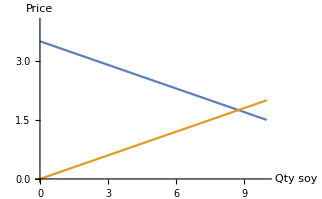

```mathematica
Plot[{Derbs,Dercs},{qs, 0, 10}, AxesLabel->{"Qty soy","Price"}, PlotRange->{0,4}]
```

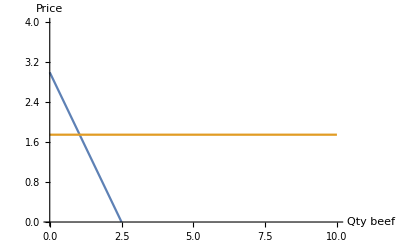

```mathematica
Plot[{Derbb,0.2*8.75},{qb, 0, 10}, AxesLabel->{"Qty beef","Price"}, PlotRange->{0,4}]
```

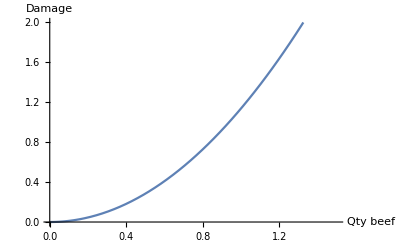

```mathematica
Plot[dbb,{qb, 0,1.5},  AxesLabel->{"Qty beef","Damage"},  PlotRange->{0,2}]
```

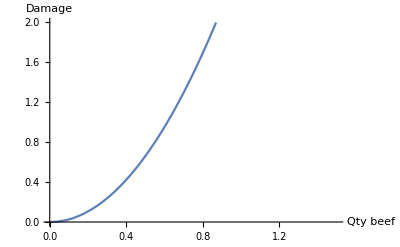

```mathematica
Plot[dbe,{qb, 0,1.5},  AxesLabel->{"Qty beef","Damage"},PlotRange->{0,2}]
```

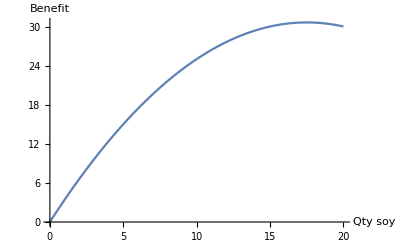

```mathematica
Plot[bs,{qs, 0,20},  AxesLabel->{"Qty soy","Benefit"}]
```

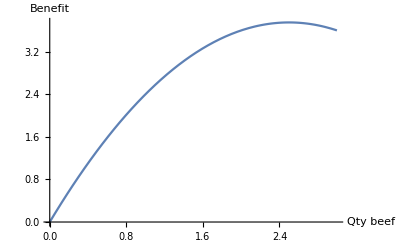

```mathematica
Plot[bb,{qb, 0,3},  AxesLabel->{"Qty beef","Benefit"}]
```

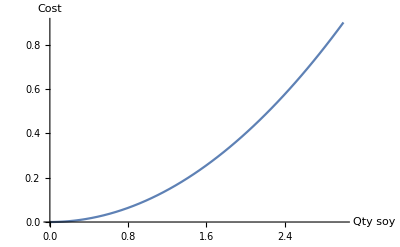

```mathematica
Plot[cs,{qs, 0,3},  AxesLabel->{"Qty soy","Cost"}]
```

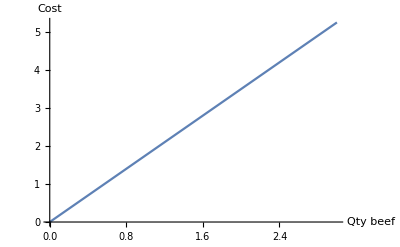

```mathematica
Plot[cb/.qs-> 8.75,{qb, 0,3},  AxesLabel->{"Qty beef","Cost"}]
```